```mathematica
(*Electronic entropy VFE contribution*)
(*Zr32C32->C+Zr32C31*)
(*S_el[Zr32C31]-S_el[Zr32C31]*)
(*Linear approximation entropy is S=Pi/3 * k_B^2 * T * DOSatEF   *) 
natms=64;
```

```mathematica
kb=0.08617332478/1000;(*in eV*)
eV2ryd=0.073498618
(*The DOS in the perfect ZrC at the zero T structure in states per eV/cell is:*)
perfDOSt0=(7.7)/natms
perfDOSt[t_]:=(7.7+((250/13.6)/4000)t)/natms
(*Lets assume the extreme case of MIT, so that the C vacancy DOS goes to zero*)
(*cvacDOSt0=(0.6493*10^1)/natms*)
```

0.0734986

0.120313

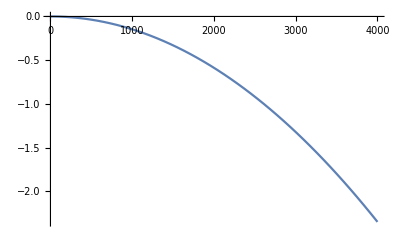

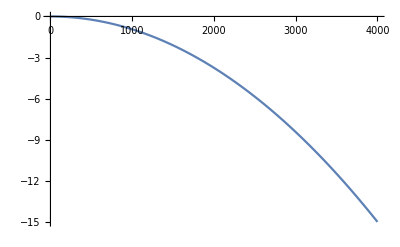

```mathematica
(*Define electronic entropy function in meV*)
elentfree[T_]:=-1000*(Pi/3)*kb^2*(perfDOSt0-cvacDOSt0)*T^2
Table[elentfree[T],{T,1,4001,500}];
Plot[elentfree[T],{T,1,4001}]
Plot[perfFree[T],{T,1,4001}]
```

## Output;

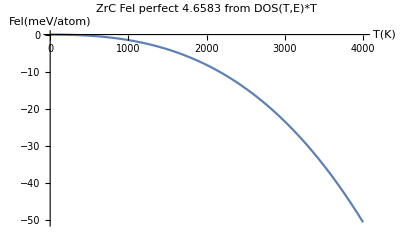

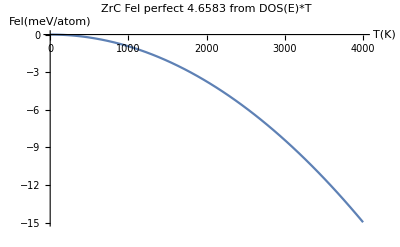

```mathematica
perfFree2[T_]:=-1000*(Pi/3)*kb^2*Evaluate@(perfDOSt[T])*T^2
Plot[perfFree2[T],{T,1,4001},AxesLabel->{"T(K)","Fel(meV/atom)"},PlotLabel->" ZrC Fel perfect 4.6583 from DOS(T,E)*T"]

perfFree[T_]:=-1000*(Pi/3)*kb^2*(perfDOSt0)*T^2
Plot[perfFree[T],{T,1,4001},AxesLabel->{"T(K)","Fel(meV/atom)"},PlotLabel->"ZrC Fel perfect 4.6583 from DOS(E)*T"]
```

```mathematica
perfFree[3829]
perfFree2[3829]
```

-13.7169

-45.0636